```mathematica
sigma=1.786;
mu=-2.649;
xx[m_,rho_]:=(6*m/(Pi*rho))^(1/3)
Nd[x_,rho_]:=6/(Pi*rho*sigma*Sqrt[2*Pi])*Erfc[(Log[x]-mu+3*sigma^2)/(Sqrt[2]*sigma)]*Exp[-3*mu+9*sigma^2/2]
Nm[m_,rho_]:=Nd[xx[m,rho],rho]
Ndn[x_,rho_,xmax_]:=Nd[xmax,rho]/Nd[x,rho]
Nmn[m_,rho_,mmax_]:=Nm[mmax,rho]/Nm[m,rho]
indexd[xmin_,xmax_,rho_]:=(Log[1]-Log[Ndn[xmin,rho,xmax]])/(Log[xmax]-Log[xmin])
index[mmin_,mmax_,rho_]:=(Log[1]-Log[Nmn[mmin,rho,mmax]])/(Log[mmax]-Log[mmin])
```

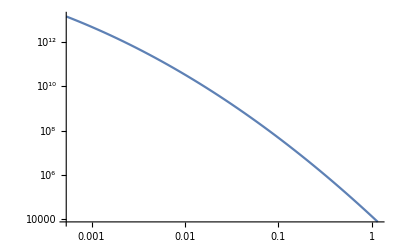

```mathematica
LogLogPlot[Nd[x,rho1],{x,(6*10^-13/1000/(Pi*rho1))^(1/3),(6*10^-3/1000/(Pi*rho1))^(1/3)}]
```

```mathematica
(6*10^-13/1000/(Pi*rho1))^(1/3)
Nd[(6*10^-13/1000/(Pi*rho1))^(1/3),rho1]
(6*10^-3/1000/(Pi*rho1))^(1/3)
Nd[(6*10^-3/1000/(Pi*rho1))^(1/3),rho1]
```

0.000536035

1.44693×10^13

1.15485

7431.52

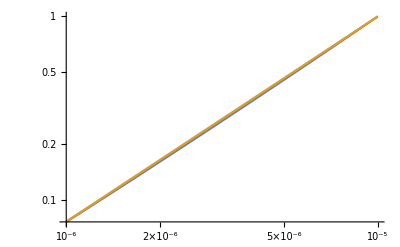

```mathematica
rho1=1.24*10^-6;
mmax=10^-5;
LogLogPlot[{Ndn[(6*m/1000/(Pi*rho1))^(1/3),rho1,(6*mmax/1000/(Pi*rho1))^(1/3)],(m/mmax)^(1.12)},{m,10^-6,mmax}]
```

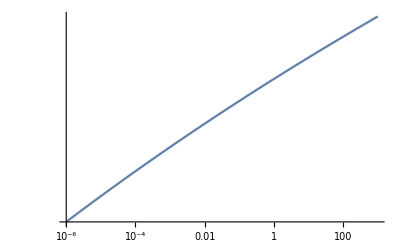

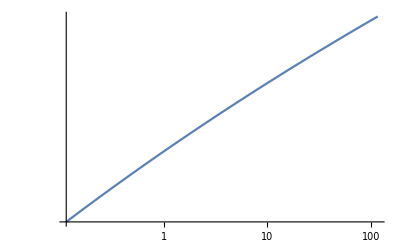

```mathematica
rho1=1.24*10^-3;
mmin=10^-6;
mmax=10^3;
LogLogPlot[index[mmin,m,rho1],{m,mmin,mmax}]
LogLogPlot[indexd[xx[mmin,rho1],x,rho1],{x,xx[mmin,rho1],xx[mmax,rho1]}]
```

```mathematica
Nd[(6*m/1000/(Pi*rho1))^(1/3),rho1]/.m->10^-11
Nd[(6*m/1000/(Pi*rho1))^(1/3),rho1]/.m->10^-3
```

8.23792×10^11

7431.52